# Практикум 7

Выполнила студентка ММФ БГУ
КМ, 1 к, 5 гр . Ковалевская В . С .
  9   декабря 2021

### 6.1

```mathematica
R2C[{x_,y_}]:=x+ⅈ y;
C2R[z_]:={Re@z,Im@z};
```

```mathematica
R2C[{1,5}]
```

1+5 ⅈ

```mathematica
C2R[1+5 ⅈ]
```

{1,5}

```mathematica
TaskSubs[zz_Graphics,f_]:=zz/.{Point[P_]:>(P//R2C//f//C2R//Point),(h:Line|Polygon)[P_]:>h[(#//R2C//f//C2R)&/@P]};
```

```mathematica
ClearAll[ShowConform];
ShowConform[f_,g_Graphics,opts___]:=GraphicsGrid[{{g,TaskSubs[g,f]}},opts]
```

### 6.2. Полярная координатная сетка.

```mathematica
Range[0,2 π,π/4]
```

{0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

```mathematica
Range[0,1,.2]
```

{0.,0.2,0.4,0.6,0.8,1.}

```mathematica
Outer[#1 {Cos[#2],Sin[#2]}&,Range[0,1,.2],Range[0,2 π,π/4]]
```

{{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}},{{0.2,0.},{0.141421,0.141421},{0.,0.2},{-0.141421,0.141421},{-0.2,0.},{-0.141421,-0.141421},{0.,-0.2},{0.141421,-0.141421},{0.2,0.}},{{0.4,0.},{0.282843,0.282843},{0.,0.4},{-0.282843,0.282843},{-0.4,0.},{-0.282843,-0.282843},{0.,-0.4},{0.282843,-0.282843},{0.4,0.}},{{0.6,0.},{0.424264,0.424264},{0.,0.6},{-0.424264,0.424264},{-0.6,0.},{-0.424264,-0.424264},{0.,-0.6},{0.424264,-0.424264},{0.6,0.}},{{0.8,0.},{0.565685,0.565685},{0.,0.8},{-0.565685,0.565685},{-0.8,0.},{-0.565685,-0.565685},{0.,-0.8},{0.565685,-0.565685},{0.8,0.}},{{1.,0.},{0.707107,0.707107},{0.,1.},{-0.707107,0.707107},{-1.,0.},{-0.707107,-0.707107},{0.,-1.},{0.707107,-0.707107},{1.,0.}}}

```mathematica
Outer[#1 {Cos[#2],Sin[#2]}&,Range[0,1,.2],Range[0,2 π,π/4]]//MatrixForm
```

((0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.)
(0.2
0.) | (0.141421
0.141421) | (0.
0.2) | (-0.141421
0.141421) | (-0.2
0.) | (-0.141421
-0.141421) | (0.
-0.2) | (0.141421
-0.141421) | (0.2
0.)
(0.4
0.) | (0.282843
0.282843) | (0.
0.4) | (-0.282843
0.282843) | (-0.4
0.) | (-0.282843
-0.282843) | (0.
-0.4) | (0.282843
-0.282843) | (0.4
0.)
(0.6
0.) | (0.424264
0.424264) | (0.
0.6) | (-0.424264
0.424264) | (-0.6
0.) | (-0.424264
-0.424264) | (0.
-0.6) | (0.424264
-0.424264) | (0.6
0.)
(0.8
0.) | (0.565685
0.565685) | (0.
0.8) | (-0.565685
0.565685) | (-0.8
0.) | (-0.565685
-0.565685) | (0.
-0.8) | (0.565685
-0.565685) | (0.8
0.)
(1.
0.) | (0.707107
0.707107) | (0.
1.) | (-0.707107
0.707107) | (-1.
0.) | (-0.707107
-0.707107) | (0.
-1.) | (0.707107
-0.707107) | (1.
0.))

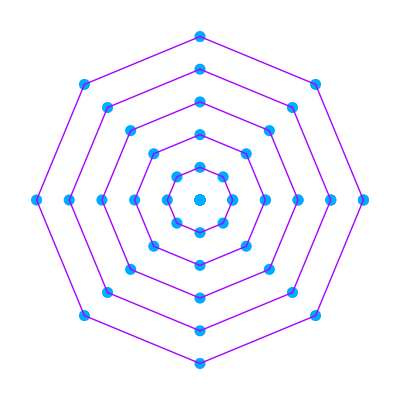

```mathematica
Graphics[{{Hue[5/9],PointSize[0.02],Map[Point,#1,{2}]},{Hue[7/9],Line/@#1}}&[Outer[#1 {Cos[#2],Sin[#2]}&,Range[0,1,.2],Range[0,2 π,π/4]]]]
```

```mathematica
PolarMesh[r_,{nr_,nϕ_}]:=({{Hue[5/9],PointSize[0.02],Map[Point,#1,{2}]},{Hue[7/9],Map[Line,#1,{1}]}}&)[Table[ρ {Cos[ϕ],Sin[ϕ]},{ρ,0,r,r/nr},{ϕ,0,2 π,(2 π)/nϕ}]]
```

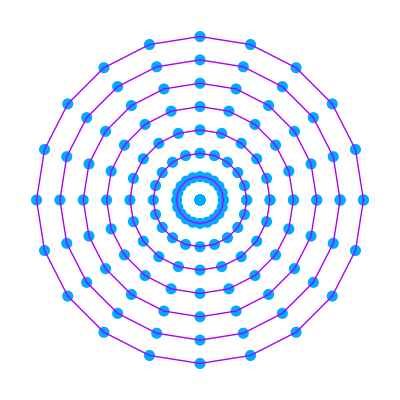

```mathematica
Graphics[PolarMesh[1,{7,20}]]
```

### 6.3. Сетка декартовых координат

```mathematica
M=Table[x+ⅈ y,{x,0,1,.2},{y,0,1,.2}]
```

{{0.+0. ⅈ,0.+0.2 ⅈ,0.+0.4 ⅈ,0.+0.6 ⅈ,0.+0.8 ⅈ,0.+1. ⅈ},{0.2+0. ⅈ,0.2+0.2 ⅈ,0.2+0.4 ⅈ,0.2+0.6 ⅈ,0.2+0.8 ⅈ,0.2+1. ⅈ},{0.4+0. ⅈ,0.4+0.2 ⅈ,0.4+0.4 ⅈ,0.4+0.6 ⅈ,0.4+0.8 ⅈ,0.4+1. ⅈ},{0.6+0. ⅈ,0.6+0.2 ⅈ,0.6+0.4 ⅈ,0.6+0.6 ⅈ,0.6+0.8 ⅈ,0.6+1. ⅈ},{0.8+0. ⅈ,0.8+0.2 ⅈ,0.8+0.4 ⅈ,0.8+0.6 ⅈ,0.8+0.8 ⅈ,0.8+1. ⅈ},{1.+0. ⅈ,1.+0.2 ⅈ,1.+0.4 ⅈ,1.+0.6 ⅈ,1.+0.8 ⅈ,1.+1. ⅈ}}

```mathematica
z1=Map[{Re@#,Im@#}&,M,{2}]
```

{{{0.,0.},{0.,0.2},{0.,0.4},{0.,0.6},{0.,0.8},{0.,1.}},{{0.2,0.},{0.2,0.2},{0.2,0.4},{0.2,0.6},{0.2,0.8},{0.2,1.}},{{0.4,0.},{0.4,0.2},{0.4,0.4},{0.4,0.6},{0.4,0.8},{0.4,1.}},{{0.6,0.},{0.6,0.2},{0.6,0.4},{0.6,0.6},{0.6,0.8},{0.6,1.}},{{0.8,0.},{0.8,0.2},{0.8,0.4},{0.8,0.6},{0.8,0.8},{0.8,1.}},{{1.,0.},{1.,0.2},{1.,0.4},{1.,0.6},{1.,0.8},{1.,1.}}}

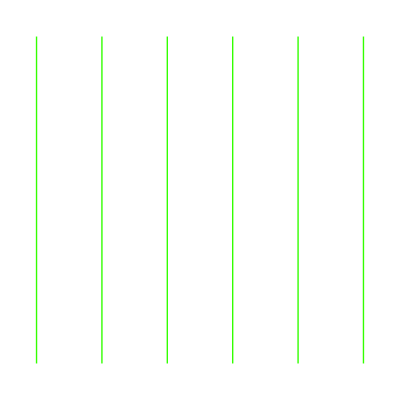

```mathematica
Graphics[{{Hue[.3],Line[#]}&/@z1}]
```

```mathematica
Transpose[z1];
```

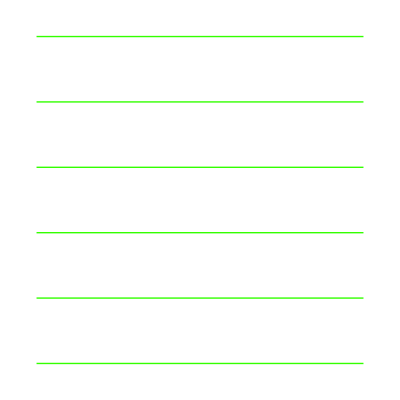

```mathematica
Graphics[{{Hue[.3],Line[#]}&/@Transpose[z1]}]
```

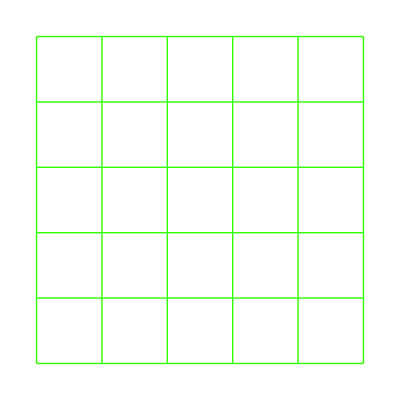

```mathematica
Graphics[{{Hue[.3],Line[#]}&/@z1,{Hue[.3],Line[#]}&/@Transpose[z1]}]
```

```mathematica
Graphics[{{Hue[.3],Line[#]}&/@#,{Hue[.3],Line[#]}&/@Transpose[#]}&@Map[{Re@#,Im@#}&,Table[x+ⅈ y,{x,0,1,.2},{y,0,1,.2}],{2}]]
```

-Graphics-

```mathematica
SquareGrid[{z0_,z1_},{n0_,n1_}]:=Graphics[{{Hue[.3],Line[#]}&/@#,{Hue[.3],Line[#]}&/@Transpose[#]}&@Map[{Re@#,Im@#}&,Table[((n0-i0) Re[z0]+i0 Re[z1])/n0+ⅈ ((n1-i1) Re[z0]+i1 Re[z1])/n1,{i0,0,n0},{i1,0,n1}],{2}]]
```

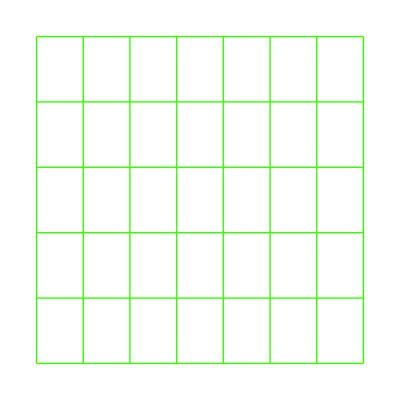

```mathematica
SquareGrid[{1+5 ⅈ ,-2-ⅈ},{7,5}]
```

```mathematica
CartesianMesh[{z0_,z1_},{n0_,n1_}]:=Module[{Ν},{Ν=Length[#];MapIndexed[{Hue[((Ν-#2[[1]]) 4/6+#2[[1]] 3/6)/Ν],Line[#1]}&,#],MapIndexed[{Hue[((Ν-#2[[1]]) 4/6+#2[[1]] 3/6)/Ν],Line[#1]}&,#//Transpose]}&@Map[{Re@#,Im@#}&,Table[((n0-i0) Re[z0]+i0 Re[z1])/n0+ⅈ ((n1-i1) Re[z0]+i1 Re[z1])/n1,{i0,0,n0},{i1,0,n1}],{2}]]
```

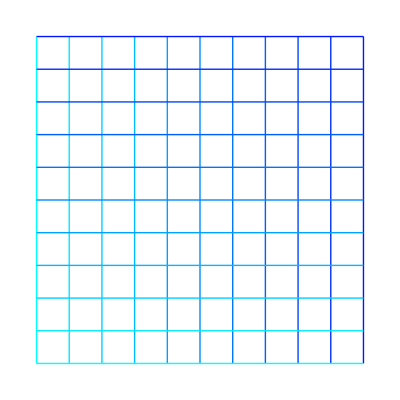

```mathematica
Graphics[CartesianMesh[{1,ⅈ},{10,10}]]
```

### 6.10

```mathematica
ClearAll[a,z1];
a=Table[x+ⅈ y,{x,1,√2,.1},{y,π/4,π/2,.1}]
```

{{1.+0.785398 ⅈ,1.+0.885398 ⅈ,1.+0.985398 ⅈ,1.+1.0854 ⅈ,1.+1.1854 ⅈ,1.+1.2854 ⅈ,1.+1.3854 ⅈ,1.+1.4854 ⅈ},{1.1+0.785398 ⅈ,1.1+0.885398 ⅈ,1.1+0.985398 ⅈ,1.1+1.0854 ⅈ,1.1+1.1854 ⅈ,1.1+1.2854 ⅈ,1.1+1.3854 ⅈ,1.1+1.4854 ⅈ},{1.2+0.785398 ⅈ,1.2+0.885398 ⅈ,1.2+0.985398 ⅈ,1.2+1.0854 ⅈ,1.2+1.1854 ⅈ,1.2+1.2854 ⅈ,1.2+1.3854 ⅈ,1.2+1.4854 ⅈ},{1.3+0.785398 ⅈ,1.3+0.885398 ⅈ,1.3+0.985398 ⅈ,1.3+1.0854 ⅈ,1.3+1.1854 ⅈ,1.3+1.2854 ⅈ,1.3+1.3854 ⅈ,1.3+1.4854 ⅈ},{1.4+0.785398 ⅈ,1.4+0.885398 ⅈ,1.4+0.985398 ⅈ,1.4+1.0854 ⅈ,1.4+1.1854 ⅈ,1.4+1.2854 ⅈ,1.4+1.3854 ⅈ,1.4+1.4854 ⅈ}}

```mathematica
z1=Map[{Re@#,Im@#}&,a,{2}]
```

{{{1.,0.785398},{1.,0.885398},{1.,0.985398},{1.,1.0854},{1.,1.1854},{1.,1.2854},{1.,1.3854},{1.,1.4854}},{{1.1,0.785398},{1.1,0.885398},{1.1,0.985398},{1.1,1.0854},{1.1,1.1854},{1.1,1.2854},{1.1,1.3854},{1.1,1.4854}},{{1.2,0.785398},{1.2,0.885398},{1.2,0.985398},{1.2,1.0854},{1.2,1.1854},{1.2,1.2854},{1.2,1.3854},{1.2,1.4854}},{{1.3,0.785398},{1.3,0.885398},{1.3,0.985398},{1.3,1.0854},{1.3,1.1854},{1.3,1.2854},{1.3,1.3854},{1.3,1.4854}},{{1.4,0.785398},{1.4,0.885398},{1.4,0.985398},{1.4,1.0854},{1.4,1.1854},{1.4,1.2854},{1.4,1.3854},{1.4,1.4854}}}

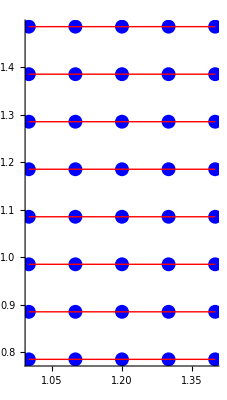

```mathematica
Graphics[({{Hue[2/3],PointSize[0.025],Map[Point,#,{2}]},{Hue[0],Map[Line,#,{1}]}}&)[Transpose[z1]],AspectRatio->Full,Axes->True]
```

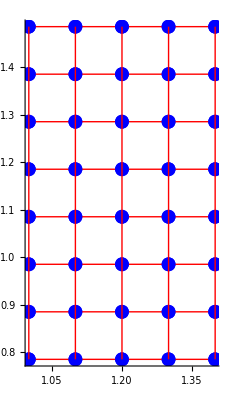

```mathematica
grz=Graphics[{({{Hue[2/3],PointSize[0.025],Map[Point,#,{2}]},{Hue[0],Map[Line,#,{1}]}}&)[Transpose[z1]],({{Hue[2/3],PointSize[0.025],Map[Point,#,{2}]},{Hue[0],Map[Line,#,{1}]}}&)[z1]},AspectRatio->Full,Axes->True]
```

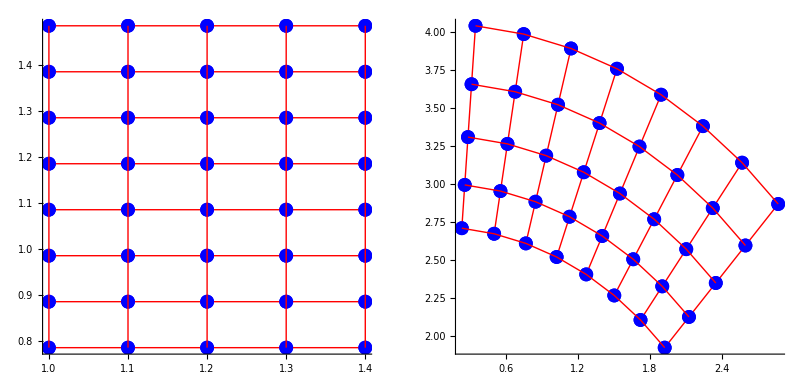

```mathematica
ShowConform[ⅇ^#&,grz]
```

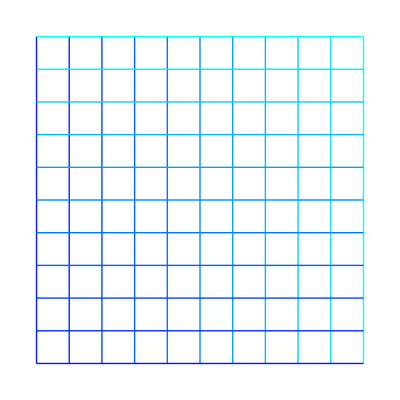

```mathematica
zzz=Graphics[CartesianMesh[{1+ⅈ 0.785, 1.4+1.486ⅈ},{10,10}]]
```

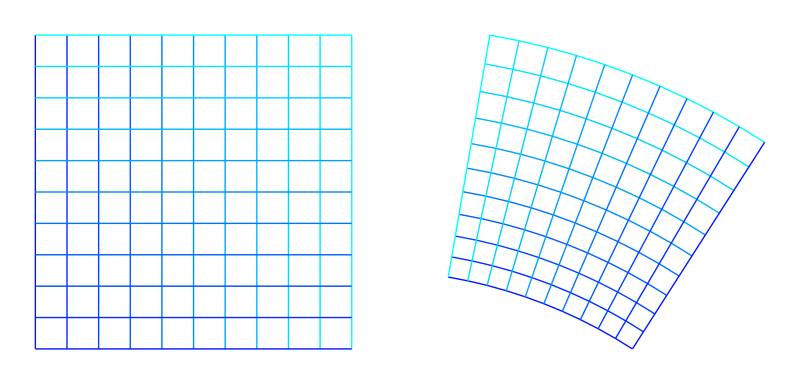

```mathematica
ShowConform[ⅇ^#&,zzz]
```

```mathematica
Table[{Hue[((Length[z1] i) 1/3)/Length[z1]],PointSize@0.05,Map[Point,z1,{2}]},{i,1,6}];
```

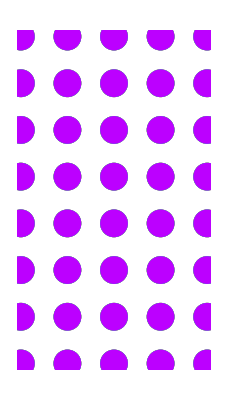

```mathematica
Graphics[{Table[{Hue[((Length[z1] i) 5/19)/Length[z1]],PointSize@0.05,Map[Point,z1,{2}]},{i,0,3}]}]
```

```mathematica
Table[{Hue[((Length[z1] i) 1/3)/Length[z1]],Line@z1},{i,0,3}];
```

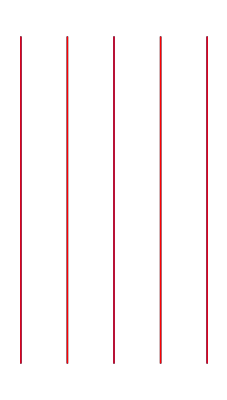

```mathematica
Graphics[{Table[{Hue[((Length[z1] i) 1/3)/Length[z1]],Line@z1},{i,0,3}]}]
```

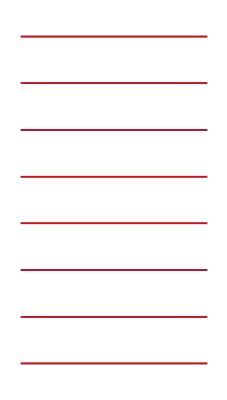

```mathematica
Graphics[{Table[{Hue[((Length[Transpose[z1]] i) 1/3)/Length[Transpose[z1]]],Line[Transpose[z1]]},{i,0,3}]}]
```

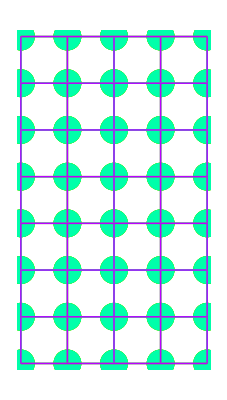

```mathematica
Graphics[{Table[{Hue[((Length[z1] i) 2/27)/Length[z1]],PointSize@0.05,Map[Point,z1,{2}]},{i,1,6}],Table[{Hue[((Length[z1] i) 5/19)/Length[z1]],Line@z1},{i,0,3}],Table[{Hue[((Length[Transpose[z1]] i) 5/19)/Length[Transpose[z1]]],Line[Transpose[z1]]},{i,0,3}]}]
```

```mathematica
CartMesh[{{x0_,y0_},{x1_,y1_}},{n0_,n1_}]:=({Table[{Hue[((Length[#] i) 2/27)/Length[#]],PointSize@0.05,Map[Point,#,{2}]},{i,1,n0}],Table[{Hue[((Length[#] i) 5/19)/Length[#]],Line@#},{i,0,n1}],Table[{Hue[((Length[Transpose[#]] i) 5/19)/Length[Transpose[#]]],Line[Transpose[#]]},{i,0,n1}]})&@Map[{Re@#,Im@#}&,Table[x+ⅈ y,{x,x0,x1,.1},{y,y0,y1,.1}],{2}]
```

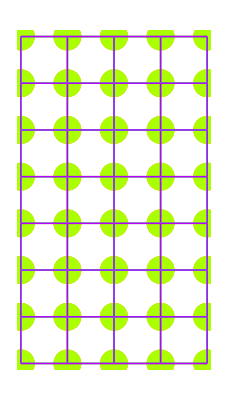

```mathematica
Graphics[CartMesh[{{1,π/4},{√2,π/2}},{3,3}]]
```

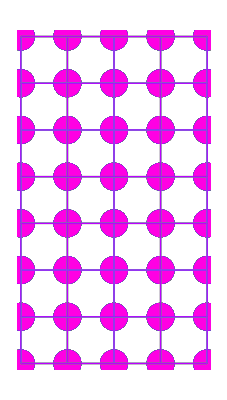

```mathematica
zz=Graphics[CartMesh[{{1,0.785},{√2,1.57}},{79,3}]]
```